# Invasion condition and mate choice bias

This Mathematica notebook generates figures for section “Additional Method” where condition for invasion for Medea and Distortion gene drive are derived.

## Three cases (p=0.5, p=0.75, p=1)

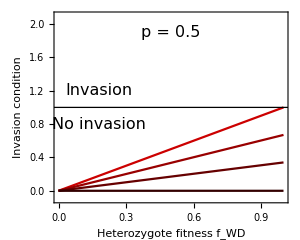

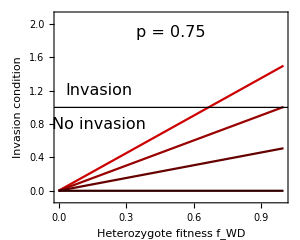

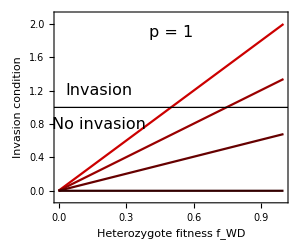

```mathematica
p=0.5;
Plot[Evaluate[Table[(2 p(1-h) fwd)/fww/.{fww->1},{h,{0,0.33,0.66,1.0}}]],{fwd,0,1},GridLines->{None, {1}},PlotRange->{Automatic,{-0.1,2.1}},Frame->True,GridLinesStyle->Directive[ Black,Thickness[0.003]],FrameStyle->Directive[Black,Thickness[0.002],FontSize->12],FrameLabel->{Style["Heterozygote fitness f_WD",Black,16],Style[ "Invasion condition",Black,16]},PlotStyle->{Darker[Red,0.2],Darker[Red,0.4],Darker[Red,0.6],Darker[Red,0.8]},Epilog->{Inset[Style["No invasion",16],{0.18,0.8}],Inset[Style["Invasion",16],{0.18,1.2}],Inset[Style["p = "<>ToString[p],16],{0.5,1.9}]},ImageSize->300,AspectRatio->0.8]

p=0.75;
Plot[Evaluate[Table[(2 p(1-h) fwd)/fww/.{fww->1},{h,{0,0.33,0.66,1.0}}]],{fwd,0,1},GridLines->{None, {1}},PlotRange->{Automatic,{-0.1,2.1}},Frame->True,GridLinesStyle->Directive[ Black,Thickness[0.003]],FrameStyle->Directive[Black,Thickness[0.002],FontSize->12],FrameLabel->{Style["Heterozygote fitness f_WD",Black,16],Style[ "Invasion condition",Black,16]},PlotStyle->{Darker[Red,0.2],Darker[Red,0.4],Darker[Red,0.6],Darker[Red,0.8]},Epilog->{Inset[Style["No invasion",16],{0.18,0.8}],Inset[Style["Invasion",16],{0.18,1.2}],Inset[Style["p = "<>ToString[p],16],{0.5,1.9}]},ImageSize->300,AspectRatio->0.8]
p=1;
Plot[Evaluate[Table[(2 p(1-h) fwd)/fww/.{fww->1},{h,{0,0.33,0.66,1.0}}]],{fwd,0,1},GridLines->{None, {1}},PlotRange->{Automatic,{-0.1,2.1}},Frame->True,GridLinesStyle->Directive[ Black,Thickness[0.003]],FrameStyle->Directive[Black,Thickness[0.002],FontSize->12],FrameLabel->{Style["Heterozygote fitness f_WD",Black,16],Style[ "Invasion condition",Black,16]},PlotStyle->{Darker[Red,0.2],Darker[Red,0.4],Darker[Red,0.6],Darker[Red,0.8]},Epilog->{Inset[Style["No invasion",16],{0.18,0.8}],Inset[Style["Invasion",16],{0.18,1.2}],Inset[Style["p = "<>ToString[p],16],{0.5,1.9}]},ImageSize->300,AspectRatio->0.8]
```